# SpinDynamica 2D NMR Tutorial 03: Double-Quantum Filtered COSY (DQF-COSY)

## Simultaneous Pure-Absorption Diagonal and Cross Peaks, Coherence-Order Filtration, Phase Cycling, Singlet Suppression, and Active vs. Passive Couplings

## 0. Setup and Loading SpinDynamica

Evaluate both setup cells in order. Cell 1 locates the SpinDynamica repository root upward from NotebookDirectory[] using System` symbols only and loads SpinDynamica`; Cell 2 verifies that the public 2D simulation, processing, and coherence-order filtration functions are loaded.

```mathematica
nbRepoRoot=Quiet[Check[NotebookDirectory[],Directory[]]];
While[StringQ[nbRepoRoot]&&nbRepoRoot=!=""&&!FileExistsQ[FileNameJoin[{nbRepoRoot,"SpinDynamica","SpinDynamica.m"}]],With[{parent=ParentDirectory[nbRepoRoot]},If[parent===nbRepoRoot,nbRepoRoot=Directory[];Break[],nbRepoRoot=parent]]];
If[FileExistsQ[FileNameJoin[{nbRepoRoot,"SpinDynamica","SpinDynamica.m"}]],Needs["SpinDynamica`",FileNameJoin[{nbRepoRoot,"SpinDynamica","SpinDynamica.m"}]],Needs["SpinDynamica`"]];
```

SpinDynamica version SDv4.0.0 (modified by Google Anti-Gravity Neon) loaded by Mathematica 14.3 running on Microsoft Windows (64-bit).

SetUserLevel::ini: The user level is being initialized to 2. The user level may be set to an integer between 1 and 3 by using SetUserLevel[level]. Low user levels provide strong syntax trapping at the expense of slow execution for some routines. High user levels relax the syntax trapping in order to provide better execution speeds.

SetUserLevel::ul: The user level has been set to 2.

SetUserLevel::modsymbs: Additional definitions have been given to the following symbols: {Commutator,Duration,Exp,Expand,Plus,Power,Simplify,SolidAngle,Times,WignerD}

```mathematica
{MemberQ[$Packages,"Signals`Signal2D`"],MemberQ[$Packages,"Simulations`Signal2D`"],Context[Signal2D],Context[CoherenceOrderFiltration]}
```

{True,True,Simulations`Signal2D`,Events`PulseSequence`}

## 1. Why Double-Quantum Filtering? The COSY-90 Phase Trade-Off

In Tutorial 01 we simulated a simple 90-t1-90 COSY-90 experiment on a weakly coupled two-spin-1/2 AX system (chemical shifts -120 Hz and +180 Hz, scalar coupling J = 24 Hz). That simple sequence reveals a fundamental constraint of two-pulse COSY:
  - The cross-peak coherence pathways originate as anti-phase magnetization (~ sin(Pi J t1) sin(Pi J t2)).
  - The diagonal-peak coherence pathways remain in-phase (~ cos(Pi J t1) cos(Pi J t2)).

Because sine and cosine J-modulations differ by 90 degrees in both t1 and t2, no single phase correction can make both the cross peaks and the diagonal peaks purely absorptive at the same time.

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

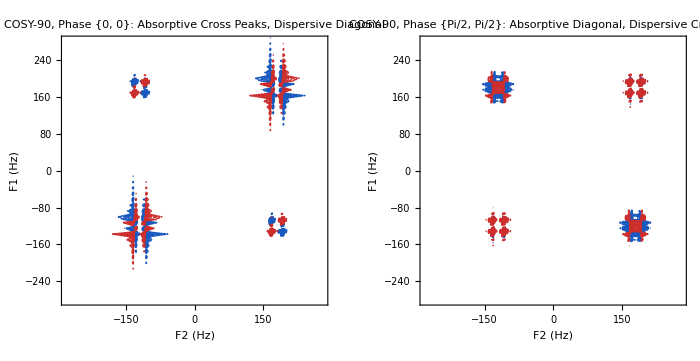

```mathematica
SetSpinSystem[{{1,1/2},{2,1/2}}];
nu1=-120.;
nu2=180.;
j12=24.;
Hax=2.*Pi*(nu1*opI[1,"z"]+nu2*opI[2,"z"]+j12*(opI[1,"z"].opI[2,"z"]));
rho0=opI["z"];
sigCosy=Signal2D[{{{2Pi800.,64}},{{2Pi800.,128}}},InitialDensityOperator->rho0,Preparation->Pulse[{Pi/2,"x"}],Mixing->Pulse[{Pi/2,"x"}],BackgroundGenerator->Hax,LineBroadening->16.];
specCosyCross=FT[sigCosy,ZeroFill->{2,2}];
specCosyDiag=PhaseSpectrum2D[specCosyCross,{Pi/2,Pi/2}];
GraphicsRow[{PlotSpectrum2D[specCosyCross,PlotRange->{{-280,280},{-280,280}},PlotLabel->"COSY-90, Phase {0, 0}:\nAbsorptive Cross Peaks, Dispersive Diagonal",ImageSize->320],PlotSpectrum2D[specCosyDiag,PlotRange->{{-280,280},{-280,280}},PlotLabel->"COSY-90, Phase {Pi/2, Pi/2}:\nAbsorptive Diagonal, Dispersive Cross Peaks",ImageSize->320]},ImageSize->700,Spacings->16]
```

Notice how the broad dispersive star-shaped wings of the diagonal peaks extend far across the spectrum when phased for pure absorption cross peaks (left). In crowded spectra, those dispersive diagonal tails easily obscure nearby cross peaks. Double-Quantum Filtered COSY (DQF-COSY) solves this by placing both diagonal and cross peaks on equal anti-phase footing.

## 2. DQF-COSY with CoherenceOrderFiltration

DQF-COSY replaces the single mixing pulse with two adjacent 90-degree pulses separated by a double-quantum filter:
  90_x  -  t1  -  90_x  -  [DQF: select p in {-2, +2}]  -  90_x  -  t2

Between the second and third pulses, only double-quantum coherences (p = +/-2) are allowed to survive:
  1. Any in-phase single-quantum term remaining at the end of t1 is converted by the second 90_x pulse into longitudinal magnetization (p = 0) or single-quantum coherence (p = +/-1), so it is rejected by the filter.
  2. Only anti-phase single-quantum terms (2 I_1z I_2x,y, created by sin(Pi J t1) evolution) are rotated into two-spin double-quantum coherence (2 I_1x I_2y +/- 2 I_1y I_2x), pass through the filter, and are converted back into anti-phase single-quantum coherence by the third 90_x read pulse.

In SpinDynamica, we can place CoherenceOrderFiltration[{-2, 2}] directly inside the Mixing list. Notice from ReportSignalCalculationMethod -> True that coherence-order filtration inside Signal2D runs directly in fast Hilbert space.

Signal2D::reportscm: Using SignalCalculationMethod -> DoubleDiagonalization (Hilbert space).

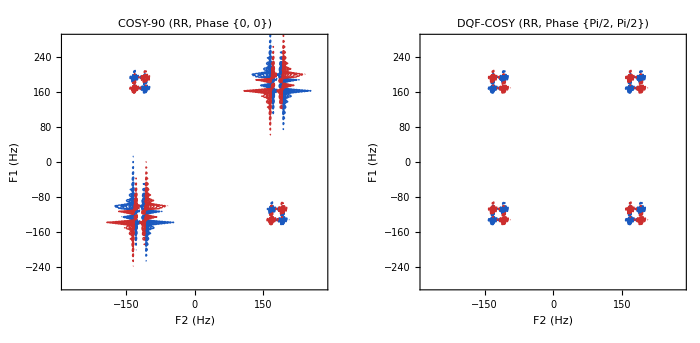

```mathematica
dqfMix={Pulse[{Pi/2,"x"}],CoherenceOrderFiltration[{-2,2}],Pulse[{Pi/2,"x"}]};
sigDQF=Signal2D[{{{2Pi800.,64}},{{2Pi800.,128}}},InitialDensityOperator->rho0,Preparation->Pulse[{Pi/2,"x"}],Mixing->dqfMix,BackgroundGenerator->Hax,LineBroadening->16.,ReportSignalCalculationMethod->True];
specDQF=FT[sigDQF,ZeroFill->{2,2},PhaseCorrection->{Pi/2,Pi/2}];
GraphicsRow[{PlotSpectrum2D[specCosyCross,PlotRange->{{-280,280},{-280,280}},BaseContourLevel->0.04,PlotLabel->"COSY-90 (RR, Phase {0, 0})",ImageSize->320],PlotSpectrum2D[specDQF,PlotRange->{{-280,280},{-280,280}},BaseContourLevel->0.04,PlotLabel->"DQF-COSY (RR, Phase {Pi/2, Pi/2})",ImageSize->320]},ImageSize->700,Spacings->16]
```

Why PhaseCorrection -> {Pi/2, Pi/2}? With all three pulses along x and QuadratureMethod -> "States", the extra 90-degree pulse through the p = +/-2 pathway introduces a Pi/2 phase shift in both dimensions relative to COSY-90. Applying PhaseCorrection -> {Pi/2, Pi/2} puts BOTH the diagonal peaks and the cross peaks into pure 2D anti-phase absorption in the "RR" component, completely removing the dispersive diagonal tails.

We can confirm this lineshape improvement directly by taking 1D F2 slices via ExtractSlice through one multiplet row of the diagonal peak (F1 = -108 Hz) and one row of the cross peak (F1 = +192 Hz).

```mathematica
sliceDiagCosy=ExtractSlice[specCosyCross,"F2",-108.,Component->"RR"];
sliceDiagDQF=ExtractSlice[specDQF,"F2",-108.,Component->"RR"];
sliceCrossCosy=ExtractSlice[specCosyCross,"F2",192.,Component->"RR"];
sliceCrossDQF=ExtractSlice[specDQF,"F2",192.,Component->"RR"];
GraphicsRow[{ListLinePlot[{sliceDiagCosy,sliceDiagDQF},PlotRange->{{-260,260},All},AspectRatio->0.55,ImageSize->350,PlotStyle->{Directive[Gray,Dashed,Thickness[0.004]],Directive[RGBColor[0.10,0.35,0.75],Thickness[0.005]]},PlotLegends->Placed[{"COSY-90 (dispersive)","DQF-COSY (absorptive)"},Above],Frame->True,FrameTicks->{{Automatic,Automatic},{{-200,-100,0,100,200},Automatic}},FrameLabel->{"F2 (Hz)","Intensity"},PlotLabel->"Diagonal Slice (F1 = -108 Hz)"],ListLinePlot[{sliceCrossCosy,sliceCrossDQF},PlotRange->{{-260,260},All},AspectRatio->0.55,ImageSize->350,PlotStyle->{Directive[Gray,Dashed,Thickness[0.004]],Directive[RGBColor[0.80,0.18,0.18],Thickness[0.005]]},PlotLegends->Placed[{"COSY-90 (cross)","DQF-COSY (cross)"},Above],Frame->True,FrameTicks->{{Automatic,Automatic},{{-200,-100,0,100,200},Automatic}},FrameLabel->{"F2 (Hz)","Intensity"},PlotLabel->"Cross-Peak Slice (F1 = +192 Hz)"]},ImageSize->760,Spacings->24]
```

-Graphics-

In the left slice (F1 = -108 Hz), the COSY-90 diagonal at F2 = -120 Hz has broad asymmetric dispersive wings, while the DQF-COSY diagonal collapses into a crisp anti-phase absorption doublet that returns cleanly to baseline â.80.94 at the same vertical position as the cross peak on the right (F2 = +180 Hz).

## 3. Implementing the Double-Quantum Filter via PhaseCycle

On a real spectrometer there is no instantaneous projector like CoherenceOrderFiltration[{-2, 2}]. Instead, double-quantum selection is achieved either with pulsed field gradients or by co-adding transients in a 4-step PhaseCycle.

Below we demonstrate both classic 4-step phase cycles using Signal2D's PhaseCycle option:
  1. Read-pulse cycle (pcRead): hold the first two 90_x pulses fixed and cycle the final 90-degree read pulse phase phi_3 = k Pi/2 (x, y, -x, -y) while shifting the receiver phase by -k Pi/2 (because coherence changes by Delta_p = -1 - (+/-2) = {-3, +1}, both of which satisfy Exp[-I * Delta_p * phi_3] = Exp[-I * k Pi/2], and Signal2D applies Exp[-I * ReceiverPhase]).
  2. Excitation-pulse cycle (pcPrepMix): cycle BOTH the preparation pulse and the second conversion pulse together by k Pi/2 (so double-quantum coherence acquires phase +/-2 * k Pi/2 = k Pi) while alternating the receiver phase by k Pi (0, Pi, 0, Pi).

```mathematica
pcRead=Table[<|"Mixing"->{Pulse[{Pi/2,"x"}],Pulse[{Pi/2,k*Pi/2}]},"ReceiverPhase"->-k*Pi/2|>,{k,0,3}];
pcPrepMix=Table[<|"Preparation"->Pulse[{Pi/2,k*Pi/2}],"Mixing"->{Pulse[{Pi/2,k*Pi/2}],Pulse[{Pi/2,"x"}]},"ReceiverPhase"->k*Pi|>,{k,0,3}];
sigDQFRead=Signal2D[{{{2Pi800.,64}},{{2Pi800.,128}}},InitialDensityOperator->rho0,Preparation->Pulse[{Pi/2,"x"}],BackgroundGenerator->Hax,PhaseCycle->pcRead,LineBroadening->16.];
sigDQFPrepMix=Signal2D[{{{2Pi800.,64}},{{2Pi800.,128}}},InitialDensityOperator->rho0,BackgroundGenerator->Hax,PhaseCycle->pcPrepMix,LineBroadening->16.];
Dataset[{<|"Implementation"->"4-step Read-Pulse Cycle","Max |Cos - Ideal|"->Max[Abs[sigDQFRead["Cos"]-sigDQF["Cos"]]],"Max |Sin - Ideal|"->Max[Abs[sigDQFRead["Sin"]-sigDQF["Sin"]]]|>,<|"Implementation"->"4-step Prep+Conversion Cycle","Max |Cos - Ideal|"->Max[Abs[sigDQFPrepMix["Cos"]-sigDQF["Cos"]]],"Max |Sin - Ideal|"->Max[Abs[sigDQFPrepMix["Sin"]-sigDQF["Sin"]]]|>}]
```

On a two-spin system, both 4-step phase cycles match CoherenceOrderFiltration[{-2, 2}] to machine precision (~10^-16). Notice an important practical distinction for larger spin networks: a 4-step phase cycle selects p = +/-2 mod 4 (which includes +/-6-quantum coherences in >= 6-spin systems unless extended to more steps), whereas CoherenceOrderFiltration[{-2, 2}] selects strictly p in {-2, +2} in a single evaluation â.80.94 making CoherenceOrderFiltration ideal for fast exploratory simulations, and PhaseCycle ideal when testing real spectrometer phase tables or finite/imperfect pulses.

## 4. Quadrature Modes and Diagnostics for DQF-COSY

Just like COSY-90, DQF-COSY works seamlessly with Signal2D's phase-sensitive indirect quadrature modes ("States", "StatesTPPI", "EchoAntiEcho", "OversampledStates"). Here we verify that "StatesTPPI" and "EchoAntiEcho" yield the exact same pure-absorption DQF-COSY spectrum when processed identically, and inspect QuadratureDiagnostics[sigDQF] to verify balanced quadrature channels with no diagnostic warnings.

```mathematica
sigDQFST=Signal2D[{{{2Pi800.,64}},{{2Pi800.,128}}},InitialDensityOperator->rho0,Preparation->Pulse[{Pi/2,"x"}],Mixing->dqfMix,BackgroundGenerator->Hax,QuadratureMethod->"StatesTPPI",LineBroadening->16.];
sigDQFEA=Signal2D[{{{2Pi800.,64}},{{2Pi800.,128}}},InitialDensityOperator->rho0,Preparation->Pulse[{Pi/2,"x"}],Mixing->dqfMix,BackgroundGenerator->Hax,QuadratureMethod->"EchoAntiEcho",LineBroadening->16.];
specDQFST=FT[sigDQFST,ZeroFill->{2,2},PhaseCorrection->{Pi/2,Pi/2}];
specDQFEA=FT[sigDQFEA,ZeroFill->{2,2},PhaseCorrection->{Pi/2,Pi/2}];
{"Max |StatesTPPI - States| (RR)"->Max[Abs[specDQFST["RR"]-specDQF["RR"]]],"Max |EchoAntiEcho - States| (RR)"->Max[Abs[specDQFEA["RR"]-specDQF["RR"]]]}
```

{Max |StatesTPPI - States| (RR)→0.,Max |EchoAntiEcho - States| (RR)→6.93889×10^-18}

```mathematica
QuadratureDiagnostics[sigDQF]//Dataset
```

## 5. Suppressing Uncoupled Singlets (Isolated Spins & Solvent)

Another major benefit of DQF-COSY is suppression of uncoupled spins (such as residual solvent signals or methyl singlets). An isolated spin-1/2 cannot support two-spin double-quantum coherence (|p| = 2 requires at least two coupled spins!), so it is completely eliminated by the double-quantum filter.

To demonstrate this, we add a third uncoupled spin-1/2 at +30 Hz to our AX pair and compare COSY-90 against both ideal CoherenceOrderFiltration DQF-COSY and 4-step PhaseCycle DQF-COSY.

```mathematica
SetSpinSystem[{{1,1/2},{2,1/2},{3,1/2}}];
H3=2.*Pi*(-120.*opI[1,"z"]+180.*opI[2,"z"]+30.*opI[3,"z"]+24.*(opI[1,"z"].opI[2,"z"]));
sig3Cosy=Signal2D[{{{2Pi800.,64}},{{2Pi800.,128}}},Preparation->Pulse[{Pi/2,"x"}],Mixing->Pulse[{Pi/2,"x"}],BackgroundGenerator->H3,LineBroadening->16.];
sig3DQF=Signal2D[{{{2Pi800.,64}},{{2Pi800.,128}}},Preparation->Pulse[{Pi/2,"x"}],Mixing->dqfMix,BackgroundGenerator->H3,LineBroadening->16.];
sig3PC=Signal2D[{{{2Pi800.,64}},{{2Pi800.,128}}},Preparation->Pulse[{Pi/2,"x"}],BackgroundGenerator->H3,PhaseCycle->pcRead,LineBroadening->16.];
spec3Cosy=FT[sig3Cosy,ZeroFill->{2,2}];
spec3DQF=FT[sig3DQF,ZeroFill->{2,2},PhaseCorrection->{Pi/2,Pi/2}];
{"Singlet Mag at (30, 30) Hz in COSY-90"->Max[Abs[ExtractSlice[spec3Cosy,"F2",30.,Component->"HypercomplexMagnitude"][[All,2]]]],"Singlet Mag at (30, 30) Hz in DQF-COSY"->spec3DQF["HypercomplexMagnitude"][[First[Ordering[Abs[spec3DQF["Frequency1"]-30.],1]],First[Ordering[Abs[spec3DQF["Frequency2"]-30.],1]]]],"Max |PhaseCycle - CoherenceOrderFiltration| (Cos)"->Max[Abs[sig3PC["Cos"]-sig3DQF["Cos"]]]}
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2},{3,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2},{3,1/2}},BasisLabels→Automatic].

{Singlet Mag at (30, 30) Hz in COSY-90→0.127653,Singlet Mag at (30, 30) Hz in DQF-COSY→4.83137×10^-7,Max |PhaseCycle - CoherenceOrderFiltration| (Cos)→1.94289×10^-16}

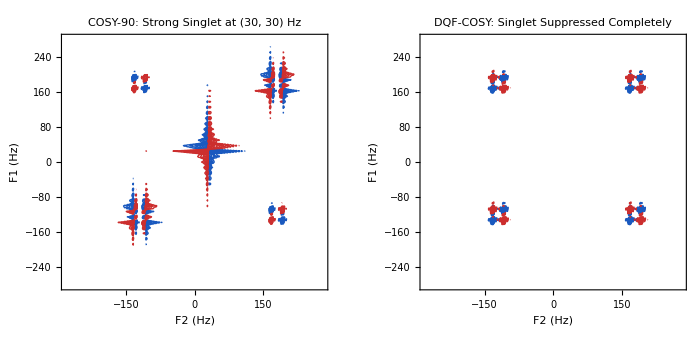

```mathematica
GraphicsRow[{PlotSpectrum2D[spec3Cosy,PlotRange->{{-280,280},{-280,280}},BaseContourLevel->0.04,PlotLabel->"COSY-90: Strong Singlet at (30, 30) Hz",ImageSize->320],PlotSpectrum2D[spec3DQF,PlotRange->{{-280,280},{-280,280}},BaseContourLevel->0.04,PlotLabel->"DQF-COSY: Singlet Suppressed Completely",ImageSize->320]},ImageSize->700,Spacings->16]
```

## 6. Active vs. Passive Couplings in a 3-Spin AMX System

Because DQF-COSY yields clean pure-absorption multiplets everywhere, it is the classic tool for measuring scalar coupling constants directly from cross-peak fine structure in multi-spin systems. Consider a linear three-spin AMX chain on the current three-spin-1/2 system:
  - nu_A = -200 Hz, nu_M = +20 Hz, nu_X = +210 Hz
  - J_AM = 36 Hz, J_MX = 16 Hz, J_AX = 0 Hz

In a cross peak between spins A and M:
  - J_AM is the ACTIVE coupling (responsible for coherence transfer between A and M): it produces an ANTI-PHASE splitting (opposite signs across the 36 Hz doublet in both F1 and F2).
  - J_MX is a PASSIVE coupling to the spectator spin X on M: it does not transfer coherence here, so along F2 (the M spin dimension) each anti-phase component is split IN-PHASE (same sign) by 16 Hz.

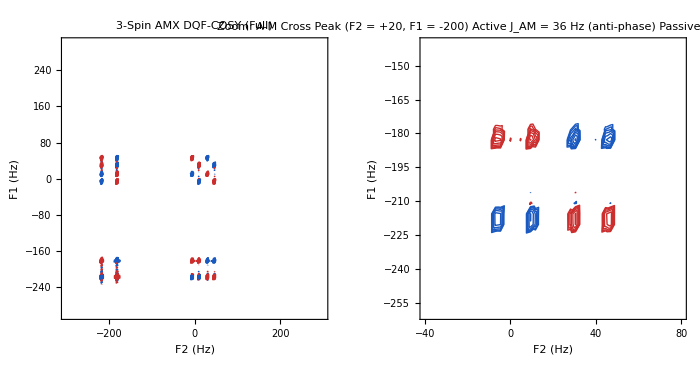

```mathematica
Hamx=2.*Pi*(-200.*opI[1,"z"]+20.*opI[2,"z"]+210.*opI[3,"z"]+36.*(opI[1,"z"].opI[2,"z"])+16.*(opI[2,"z"].opI[3,"z"]));
sigAMX=Signal2D[{{{2Pi900.,96}},{{2Pi900.,192}}},Preparation->Pulse[{Pi/2,"x"}],Mixing->dqfMix,BackgroundGenerator->Hamx,LineBroadening->10.];
specAMX=FT[sigAMX,ZeroFill->{2,2},PhaseCorrection->{Pi/2,Pi/2}];
GraphicsRow[{PlotSpectrum2D[specAMX,PlotRange->{{-300,300},{-300,300}},BaseContourLevel->0.05,PlotLabel->"3-Spin AMX DQF-COSY (Full)",ImageSize->320],PlotSpectrum2D[specAMX,PlotRange->{{-40,80},{-260,-140}},BaseContourLevel->0.06,PlotLabel->"Zoom: A-M Cross Peak (F2 = +20, F1 = -200)\nActive J_AM = 36 Hz (anti-phase)\nPassive J_MX = 16 Hz along F2 (in-phase)",ImageSize->320]},ImageSize->700,Spacings->16]
```

Look closely at the zoomed A-M cross peak on the right: along F1 (spin A, which has only J_AM = 36 Hz) there are two components of opposite sign separated by 36 Hz; along F2 (spin M, coupled to both A and X) the active J_AM = 36 Hz flips sign between left and right halves, while within each half the passive J_MX = 16 Hz splits into a SAME-SIGN (in-phase) pair separated by 16 Hz!

## 7. Linewidth and Apodization on Anti-Phase Multiplets

Because every peak in a DQF-COSY spectrum is anti-phase, line broadening that approaches or exceeds the active scalar coupling J causes adjacent positive and negative lobes to cancel destructively, collapsing peak intensity. Conversely, matched resolution-enhancing window functions such as a shifted sine-bell (Apodization -> {"SineBell", Pi/4}) preserve crisp anti-phase structure and reduce truncation ringing.

To demonstrate this cleanly without repeating the spin-dynamics simulation, we simulate one lightly damped AX DQF-COSY signal (LineBroadening -> 4 Hz) and re-process it with FT under three different apodization settings.

```mathematica
SetSpinSystem[{{1,1/2},{2,1/2}}];
sigDQFSharp=Signal2D[{{{2Pi800.,64}},{{2Pi800.,128}}},Preparation->Pulse[{Pi/2,"x"}],Mixing->dqfMix,BackgroundGenerator->Hax,LineBroadening->4.];
specApodSharp=FT[sigDQFSharp,ZeroFill->{2,2},Apodization->{"Lorentzian",6.},PhaseCorrection->{Pi/2,Pi/2}];
specApodBroad=FT[sigDQFSharp,ZeroFill->{2,2},Apodization->{"Lorentzian",32.},PhaseCorrection->{Pi/2,Pi/2}];
specApodSine=FT[sigDQFSharp,ZeroFill->{2,2},Apodization->{"SineBell",Pi/4},PhaseCorrection->{Pi/2,Pi/2}];
{"Max |RR| (Lorentzian 6 Hz)"->Max[Abs[specApodSharp["RR"]]],"Max |RR| (Lorentzian 32 Hz)"->Max[Abs[specApodBroad["RR"]]],"Max |RR| (SineBell Pi/4)"->Max[Abs[specApodSine["RR"]]]}
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

{Max |RR| (Lorentzian 6 Hz)→0.0344444,Max |RR| (Lorentzian 32 Hz)→0.0102665,Max |RR| (SineBell Pi/4)→0.0253524}

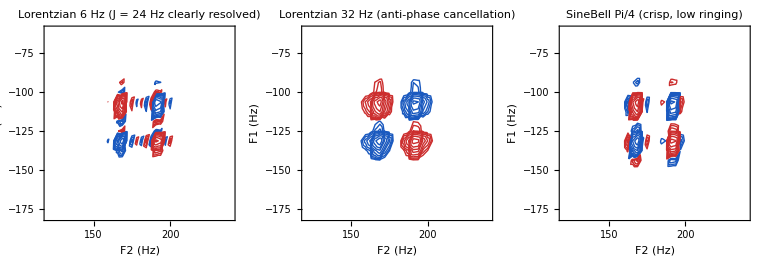

```mathematica
GraphicsRow[{PlotSpectrum2D[specApodSharp,PlotRange->{{120,240},{-180,-60}},BaseContourLevel->0.05,PlotLabel->"Lorentzian 6 Hz\n(J = 24 Hz clearly resolved)",ImageSize->230],PlotSpectrum2D[specApodBroad,PlotRange->{{120,240},{-180,-60}},BaseContourLevel->0.05,PlotLabel->"Lorentzian 32 Hz\n(anti-phase cancellation)",ImageSize->230],PlotSpectrum2D[specApodSine,PlotRange->{{120,240},{-180,-60}},BaseContourLevel->0.05,PlotLabel->"SineBell Pi/4\n(crisp, low ringing)",ImageSize->230]},ImageSize->760,Spacings->12]
```

Notice how the 32 Hz Lorentzian broadening (exceeding J = 24 Hz) both broadens the multiplet lobes and suppresses the overall peak amplitude by destructive cancellation between opposite-sign components, whereas {"SineBell", Pi/4} retains sharp resolution and suppresses t1/t2 truncation wiggles.

## 8. Summary: COSY-90 vs. DQF-COSY

When designing a 2D homonuclear correlation simulation in SpinDynamica:
  1. Use CoherenceOrderFiltration[{-2, 2}] inside Mixing for exact, fast Hilbert-space double-quantum filtering, or use PhaseCycle when modeling real spectrometer phase tables.
  2. For 90_x - t1 - 90_x - DQF - 90_x with QuadratureMethod -> "States" (or "StatesTPPI" / "EchoAntiEcho"), apply PhaseCorrection -> {Pi/2, Pi/2} so both diagonal and cross peaks appear in pure anti-phase absorption in "RR".
  3. Keep total line broadening small compared to the active coupling J to avoid anti-phase self-cancellation.

Feature | COSY-90 (2 Pulses) | DQF-COSY (3 Pulses + p = +/-2 Filter)
Pulse sequence | 90_x - t1 - 90_x - t2 | 90_x - t1 - 90_x - [DQF] - 90_x - t2
SpinDynamica Mixing | Mixing -> Pulse[{Pi/2, "x"}] | Mixing -> {Pulse[{Pi/2, "x"}], CoherenceOrderFiltration[{-2, 2}], Pulse[{Pi/2, "x"}]}
Experimental cycle | None needed for basic 2-pulse coherence | 4-step PhaseCycle on read pulse (or prep + 2nd pulse)
States PhaseCorrection | {0, 0} (cross peaks) or {Pi/2, Pi/2} (diagonal) | {Pi/2, Pi/2} (all peaks simultaneously)
Diagonal lineshape | In-phase (dispersive tails when cross peaks are absorptive) | Pure anti-phase absorption (no dispersive wings)
Cross-peak lineshape | Pure anti-phase absorption | Pure anti-phase absorption (active: anti-phase; passive: in-phase)
Uncoupled singlets | Strong dispersive diagonal peak | Suppressed completely (cannot form p = +/-2)
Sensitivity & linewidth | Full 2-pulse intensity | 50% theoretical amplitude; vanishes if linewidth >> J